# Dynamics of an Interaction between Pressure-less Dark Matter and a non-linear Dark Energy

## Vacuum Interaction

## Q = q1(x - ℛ)(1 - x)z

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z
de2:=y'=-y^2-(1/6)*(z-2*x)
de3:=z'=-3*y*z*(1-q1*(x-ℛ)*(1-x))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→2 x},{x→3 y^2,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y,z/.FPs[[2,2]]};
FP[3]={ℛ,Sqrt[ℛ/3],0};
FP[4]={ℛ,-Sqrt[ℛ/3],0};
FP[5]={ℛ,0,2*ℛ};
FP[6]={1,Sqrt[1/3],0};
FP[7]={1,-Sqrt[1/3],0};
FP[8]={1,0,2};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(3 q1 y z (-1+2 x-ℛ) | 3 q1 (-1+x) z (x-ℛ) | 3 q1 (-1+x) y (x-ℛ)
1/3 | -2 y | -1/6
-3 q1 y z (-1+2 x-ℛ) | 3 z (-1-q1 (-1+x) (x-ℛ)) | 3 y (-1-q1 (-1+x) (x-ℛ)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
2 x) | (0 | 6 q1 (-1+x) x (x-ℛ) | 0
1/3 | 0 | -1/6
0 | 6 x (-1-q1 (-1+x) (x-ℛ)) | 0) | (0
-√(x-3 q1 x^2+3 q1 x^3+3 q1 x ℛ-3 q1 x^2 ℛ)
√(x-3 q1 x^2+3 q1 x^3+3 q1 x ℛ-3 q1 x^2 ℛ)) | (1/2 | 0 | 1
-(-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)/(1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ) | (√(x (1-3 q1 x+3 q1 x^2+3 q1 ℛ-3 q1 x ℛ)))/(6 x (1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)) | 1
-(-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)/(1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ) | -(√(x (1-3 q1 x+3 q1 x^2+3 q1 ℛ-3 q1 x ℛ)))/(6 x (1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)) | 1)
(3 y^2
y
0) | (0 | 0 | 3 q1 y (-1+3 y^2) (3 y^2-ℛ)
1/3 | -2 y | -1/6
0 | 0 | 3 y (-1-q1 (-1+3 y^2) (3 y^2-ℛ))) | (0
-2 y
-3 y (1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)) | (6 y | 1 | 0
0 | 1 | 0
-(-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)/(1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ) | 1/(6 y (1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)) | 1)
(ℛ
(√ℛ)/(√3)
0) | (0 | 0 | 0
1/3 | -(2 √ℛ)/(√3) | -1/6
0 | 0 | -√3 √ℛ) | (0
-√3 √ℛ
-(2 √ℛ)/(√3)) | (2 √3 √ℛ | 1 | 0
0 | 1/(2 √3 √ℛ) | 1
0 | 1 | 0)
(ℛ
-(√ℛ)/(√3)
0) | (0 | 0 | 0
1/3 | (2 √ℛ)/(√3) | -1/6
0 | 0 | √3 √ℛ) | (0
(2 √ℛ)/(√3)
√3 √ℛ) | (-2 √3 √ℛ | 1 | 0
0 | 1 | 0
0 | -1/(2 √3 √ℛ) | 1)
(ℛ
0
2 ℛ) | (0 | 0 | 0
1/3 | 0 | -1/6
0 | -6 ℛ | 0) | (0
-√ℛ
√ℛ) | (1/2 | 0 | 1
0 | 1/(6 √ℛ) | 1
0 | -1/(6 √ℛ) | 1)
(1
1/(√3)
0) | (0 | 0 | 0
1/3 | -2/(√3) | -1/6
0 | 0 | -√3) | (-√3
-2/(√3)
0) | (0 | 1/(2 √3) | 1
0 | 1 | 0
2 √3 | 1 | 0)
(1
-1/(√3)
0) | (0 | 0 | 0
1/3 | 2/(√3) | -1/6
0 | 0 | √3) | (√3
2/(√3)
0) | (0 | -1/(2 √3) | 1
0 | 1 | 0
-2 √3 | 1 | 0)
(1
0
2) | (0 | 0 | 0
1/3 | 0 | -1/6
0 | -6 | 0) | (-1
1
0) | (0 | 1/6 | 1
0 | -1/6 | 1
1/2 | 0 | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
Eqx[q1_,ℛ_]=de1;
Eqy=de2;
Eqz[q1_,ℛ_]=de3;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[PhaseSpace13D=StreamPlot3D[{Eqx[q1,ℛ],Eqy,Eqz[q1,ℛ]},{x,ℛ,1},{y,-1.5,1.5},{z,0,1.5},AxesLabel->{"x","y","z"}],{q1,4/(1-ℛ)^2,10,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$53846'[System`VectorPlotsDump`t$53846]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$53846[0]=={0.1,-1.2,0.15,0.},WhenEvent[«1»,StopIntegration]},«4»] and NDSolveValue[{System`VectorPlotsDump`w$53846'[System`VectorPlotsDump`t$53846]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$53846[0]=={0.1,-1.2,0.15,0.},WhenEvent[«1»,StopIntegration]},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$53846,System`VectorPlotsDump`linesxmax$53846},{System`VectorPlotsDump`linesymin$53846,System`VectorPlotsDump`linesymax$53846},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$53846,System`VectorPlotsDump`linesfieldmax$53846}} and System`VectorPlotsDump`extremes$53937 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$53846,System`VectorPlotsDump`linesxmax$53846},{System`VectorPlotsDump`linesymin$53846,System`VectorPlotsDump`linesymax$53846},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$53846,System`VectorPlotsDump`linesfieldmax$53846}} and System`VectorPlotsDump`extremes$54019 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$53846'[System`VectorPlotsDump`t$53846]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$53846[0]=={0.1,-1.2,0.95,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$53846'[System`VectorPlotsDump`t$53846]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$53846[0]=={0.1,-1.2,0.95,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$53846,System`VectorPlotsDump`linesxmax$53846},{System`VectorPlotsDump`linesymin$53846,System`VectorPlotsDump`linesymax$53846},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$53846,System`VectorPlotsDump`linesfieldmax$53846}} and System`VectorPlotsDump`extremes$54093 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,«20»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,«20»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12100,System`VectorPlotsDump`linesxmax$12100},{System`VectorPlotsDump`linesymin$12100,System`VectorPlotsDump`linesymax$12100},«1»,{System`VectorPlotsDump`linesfieldmin$12100,System`VectorPlotsDump`linesfieldmax$12100}} and System`VectorPlotsDump`extremes$12154 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,0.55,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,0.55,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12100,System`VectorPlotsDump`linesxmax$12100},{System`VectorPlotsDump`linesymin$12100,System`VectorPlotsDump`linesymax$12100},«1»,{System`VectorPlotsDump`linesfieldmin$12100,System`VectorPlotsDump`linesfieldmax$12100}} and System`VectorPlotsDump`extremes$12222 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$12100'[System`VectorPlotsDump`t$12100]=={Eqx[4.,0],Eqy,Eqz[4.,0],√(Eqy^2+Eqx[«2»]^2+Eqz[«2»]^2)},System`VectorPlotsDump`w$12100[0]=={0.1,-1.2,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12100,System`VectorPlotsDump`linesxmax$12100},{System`VectorPlotsDump`linesymin$12100,System`VectorPlotsDump`linesymax$12100},«1»,{System`VectorPlotsDump`linesfieldmin$12100,System`VectorPlotsDump`linesfieldmax$12100}} and System`VectorPlotsDump`extremes$12296 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define z(x) and the first integral cz*)
α=0.5;

cz=(1/(q1*(1-ℛ))*Log[ℛ(1-α)/(α-ℛ)]-(ℛ/α)*(1+0.3111/0.6889))

z[x_,q1_,ℛ_]=(-q1)*x/q1+(1/(q1*(1-ℛ)))*Log[(x-ℛ)/(1-x)]-cz
```

-2.90318 ℛ+Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
Limit[z[x,q1,ℛ],x->ℛ]
```

(-∞)/(q1-1. q1 ℛ)

```mathematica
Limit[z[x,q1,ℛ],x->1]
```

Indeterminate

```mathematica
(*Left and right limits*)
```

```mathematica
Limit[z[x,q1,ℛ],x->ℛ,Direction->"FromAbove"]
```

(-∞)/(q1-1. q1 ℛ)

```mathematica
Limit[z[x,q1,ℛ],x->1,Direction->"FromBelow"]
```

(-∞)/(q1 (-1.+ℛ))

### Manipulate Plots

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z[x,q1,ℛ]
de2:=y'=-y^2-(1/6)*(z[x,q1,ℛ]-2*x)
de3:=z'=-3*y*z[x,q1,ℛ]*(1-q1*(x-ℛ)*(1-x))
```

```mathematica
Eqx[q1_,ℛ_,cz_]=de1;
Eqy[q1_,ℛ_,cz_]=de2;
Eqz[q1_,ℛ_,cz_]=de3;
```

```mathematica
xFP1[q1_,ℛ_]=(1/(2*(-q1)))*((-q1)*(1+ℛ)+Sqrt[(-q1)^2*(1-ℛ)^2+4*(-q1)])
```

-(√(-4 q1+q1^2 (1-ℛ)^2)-q1 (1+ℛ))/(2 q1)

```mathematica
z[x,q1,ℛ]
```

-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
(*Plot to find the possible number of Einstein points*)
Plot[z[x,4,1,.1]-2*x,{x,.1,1}]
```

-Graphics-

```mathematica
Manipulate[PhaseSpacexy=StreamPlot[{Eqx[q1,ℛ,cz],Eqy[q1,ℛ,cz]},{x,ℛ,1},{y,-1,1},Epilog->{Inset[Text[Style[(1/(q1*(1-ℛ))*Log[ℛ(1-α)/(α-ℛ)]-(ℛ/α)*(1+0.3111/0.6889)),12]],{0.2,1}]}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[z0=ContourPlot[z[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},ContourStyle->{Blue}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[Acc=ContourPlot[{2*x-z[x,q1,ℛ]==0},{x,ℛ,1},{y,-1,1},ContourStyle->{Red, Thick}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[Decn=ContourPlot[{2*x-z[x,q1,ℛ]==-.1},{x,ℛ,1},{y,-1,1},ContourStyle->{Magenta, Thick}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}];

Show[PhaseSpacexy,z0,Acc]//Dynamic
```

```mathematica
(*Plot of the range of x values for a dS fixed point*)
xdS1[ℛ_,q1_]=(1+ℛ)/2+Sqrt[(1-ℛ)^2/4-1/q1];
xdS2[ℛ_,q1_]=(1+ℛ)/2-Sqrt[(1-ℛ)^2/4-1/q1];

Manipulate[Plot[{xdS1[ℛ,q1],xdS2[ℛ,q1]},{q1,4/(1-ℛ)^2,100},PlotStyle->{Blue,Red},GridLines->{{4/(1-ℛ)^2},{ℛ,1}},GridLinesStyle->Directive[Black,Thick,Dashed],AxesLabel->{"q1","x(Fixed Point)"}],{ℛ,0,1,Appearance->"Open"}]
```

### Numeric Integration

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
ℛ=0.01
```

0.01

```mathematica
de1t:=x'[t]==-3*y[t]*q1*(x[t]-ℛ)*(1-x[t])*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)
de2t:=y'[t]==-y[t]^2-(1/6)*(((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)-2*x[t])
de3t:=z'[t]==-3*y[t]*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)*(1-q1*(x[t]-ℛ)*(1-x[t]))
```

```mathematica
(*The remaining equation when y' = y = 0, which can be solved to find the number of Einstein points admitted by the system*)
f[x_,q1_,ℛ_]=z[x,q1,ℛ]-2*x
```

-2 x+z[x,q1,0.01]

```mathematica
(*Find the limit of f when x -> ℛ*)
Limit[f[x,q1,ℛ],x->ℛ, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

Limit[-2 x+z[x,q1,0.01],x→0.01,Assumptions→{q1>4.08122,True}]

```mathematica
(*Find the limit of f when x -> 1*)
Limit[f[x,q1,ℛ],x->1, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

Limit[-2 x+z[x,q1,0.01],x→1,Assumptions→{q1>4.08122,True}]

```mathematica
(*Find derivative of f(x) with respect to x*)
fDeriv[x_,q1_,ℛ_]=Simplify[D[f[x,q1,ℛ],x]]
```

-2+z^(1,0,0)[x,q1,0.01]

```mathematica
(*Solve f'(x)=0 for q1 in limiting case*)
q1Lim[x_,ℛ_]=Solve[fDeriv[x,q1,ℛ]==0,q1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q1→InverseFunction[z^(1,0,0),2,3][x,2,0.01]}}

```mathematica
q1Lim[x_,ℛ_]=q1/.q1Lim[x,ℛ]
```

{InverseFunction[z^(1,0,0),2,3][x,2,0.01]}

```mathematica
ℛ=0.01;
```

## Plots

### No Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=15;
```

```mathematica
cz
```

cz

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[x/3+z[x,q1,ℛ]/3];
```

```mathematica
(*Plot the FFS*)
FFS0EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {Black, Thick}];
```

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.1}, {x,y},{t,-20,20}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== .1, x[0]== .99}, {x,y},{t,-20,20}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]== 0.1, x[0]==0.2}, {x,y},{t,-20,20}]; 
Traj0EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3},{t,-20,20}, PlotStyle -> {{Gray, Opacity[0.75]}}]];


(*Plot*)
(*Show[FFS0EPts,Traj0EPts]*)
```

NDSolve::dvnoarg: The function x appears with no arguments.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9992 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[«1»],NDSolve[{«1»},{x,y},{-19.9992,-20.,20.}],NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

### 2 Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=7;
```

```mathematica
cz
```

cz

```mathematica
(*Substitute q1Lim into f(x)=0 and solve for x*)
x1=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]

x2=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]
```

FindRoot::nlnum: The function value {-0.2+z[0.1,{InverseFunction[z^(1,0,0),2,3][0.1,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.2+z[0.1,{InverseFunction[z^(1,0,0),2,3][0.1,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]

FindRoot::nlnum: The function value {-1.4+z[0.7,{InverseFunction[z^(1,0,0),2,3][0.7,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.7}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-1.4+z[0.7,{InverseFunction[z^(1,0,0),2,3][0.7,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.7}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]

```mathematica
(*Find corresponding q1 values*)
q1Lim1=q1Lim[x1,ℛ]
q1Lim2=q1Lim[x2,ℛ]
```

FindRoot::nlnum: The function value {-0.2+z[0.1,{InverseFunction[z^(1,0,0),2,3][0.1,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.2+z[0.1,{InverseFunction[z^(1,0,0),2,3][0.1,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.2+z[0.1,{InverseFunction[z^(1,0,0),2,3][0.1,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{InverseFunction[z^(1,0,0),2,3][x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}],2,0.01]}

FindRoot::nlnum: The function value {-1.4+z[0.7,{InverseFunction[z^(1,0,0),2,3][0.7,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.7}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-1.4+z[0.7,{InverseFunction[z^(1,0,0),2,3][0.7,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.7}.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-1.4+z[0.7,{InverseFunction[z^(1,0,0),2,3][0.7,2.,0.01]},0.01]} is not a list of numbers with dimensions {1} at {x} = {0.7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{InverseFunction[z^(1,0,0),2,3][x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}],2,0.01]}

```mathematica
xTwoEinsteinPointsq1i=FindRoot[f[x,q1,ℛ]==0,{x,0.025}]
xTwoEinsteinPointsq1ii=FindRoot[f[x,q1,ℛ]==0,{x,0.13}]
xTwoEinsteinPointsq1iii=FindRoot[f[x,q1,ℛ]==0,{x,0.9999998}]
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

FindRoot[f[x,q1,ℛ]==0,{x,0.025}]

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

FindRoot[f[x,q1,ℛ]==0,{x,0.13}]

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

FindRoot[f[x,q1,ℛ]==0,{x,1.}]

```mathematica
0.999999889017173
```

1.

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsq1={x/.xTwoEinsteinPointsq1i,x/.xTwoEinsteinPointsq1ii,x/.xTwoEinsteinPointsq1iii}
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x/.FindRoot[f[x,q1,ℛ]==0,{x,0.025}],x/.FindRoot[f[x,q1,ℛ]==0,{x,0.13}],x/.FindRoot[f[x,q1,ℛ]==0,{x,1.}]}

```mathematica
(*Calculate the z values of the Einstein points*)
zTwoEinsteinPointsq1=z[xTwoEinsteinPointsq1,q1,ℛ]
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

z[{x/.FindRoot[f[x,q1,ℛ]==0,{x,0.025}],x/.FindRoot[f[x,q1,ℛ]==0,{x,0.13}],x/.FindRoot[f[x,q1,ℛ]==0,{x,1.}]},7,0.01]

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[1]={xTwoEinsteinPointsq1[[1]],0,zTwoEinsteinPointsq1[[1]]}
EinsteinFP[2]={xTwoEinsteinPointsq1[[2]],0,zTwoEinsteinPointsq1[[2]]}
EinsteinFP[3]={xTwoEinsteinPointsq1[[3]],0,zTwoEinsteinPointsq1[[3]]}
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x/.FindRoot[f[x,q1,ℛ]==0,{x,0.025}],0,{x/.FindRoot[f[x,q1,ℛ]==0,{x,0.025}],x/.FindRoot[f[x,q1,ℛ]==0,{x,0.13}],x/.FindRoot[f[x,q1,ℛ]==0,{x,1.}]}}

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x/.FindRoot[f[x,q1,ℛ]==0,{x,0.13}],0,7}

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x/.FindRoot[f[x,q1,ℛ]==0,{x,1.}],0,0.01}

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[(1/3)*(x+z[x,q1,ℛ])];
```

```mathematica
(*FFS reaches y = 0 at x > ℛ*)
Solve[x/3+z[x,q1,ℛ]/3==0]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[x/3+1/3 z[x,7,0.01]==0]

```mathematica
(*Plot the FFS*)
FFS2EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {{Darker[Green], Thick}}];
```

```mathematica
(*Plot the CFS*)
CFS2EPts=NDSolve[{de1t,de2t, y[0]== 0.00001, x[0]==0.023204203540973366}, {x,y},{t,-20,20}];

CFS2EPts=ParametricPlot[Evaluate[{y[t],x[t]}/.{CFS2EPts}, {t,-20,20}, PlotStyle -> {{Black, Thick}}]]
```

NDSolve::dvnoarg: The function x appears with no arguments.

ReplaceAll::reps: {NDSolve[{(-21 (1-x) (-0.01+x) y (0.690643-x+0.1443 Log[«1»]))[t]==-21 (1-x[«1»]) (-cz+0.1443 Log[«1»]-x[«1»]) (-0.01+x[t]) y[t],«2»,x[0]==0.0232042},{x,y},{t,-20,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9992 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»,{x,y},{-19.9992,-20,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -19.9992 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -19.1829 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
(*Plot the fixed points*)
FPShow2EPts=ListPlot[{{xTwoEinsteinPointsq1[[1]],0},{xTwoEinsteinPointsq1[[2]],0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
FindRoot[z[x,q1,ℛ]-2*x==0,{x,0.02}]
```

FindRoot::nlnum: The function value {-0.04+z[0.02,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.02}.

FindRoot[z[x,q1,ℛ]-2 x==0,{x,0.02}]

```mathematica
(z[x,q1,ℛ]-2*x)/.{x->0.023204203540973366}
```

-0.0464084+z[0.0232042,7,0.01]

```mathematica
(*Plot the boundary between accelerating and decelerating region*)
(*Could create Table with values of x between ℛ and 1 with small step size*)
Acc2EPts1=ContourPlot[{f[x,q1,ℛ]==0},{x,0.1,0.2} ,{y,-1,1},ContourStyle->{Red, Thick}];

Acc2EPts2=ContourPlot[{f[x,q1,ℛ]==0},{x,0.02,0.03},{y,-1,1},ContourStyle->{Red, Thick}];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
Sepx=ContourPlot[{x==ℛ,x==1},{x,0,1.1},{y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.45}, {x,y},{t,-40,40}];
```

NDSolve::dvnoarg: The function x appears with no arguments.

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.2}, {x,y},{t,-40,40}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== -0.2, x[0]== .9}, {x,y},{t,-40,40}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]==0.5, x[0]==0.011}, {x,y},{t,-40,40}]; 

Traj2EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3}, {t,-40,40}, PlotStyle -> {{Gray, Opacity[0.75]}}]];
```

NDSolve::dvnoarg: The function x appears with no arguments.

ReplaceAll::reps: {NDSolve[«1»,{x,y},{t,-40,40}],NDSolve[«1»],«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -39.9984 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{«1»},{x,y},{-39.9984,-40.,40.}],NDSolve[{«1»},{x,y},{-39.9984,-40.,40.}],NDSolve[«1»,{x,y},{-39.9984,-40.,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

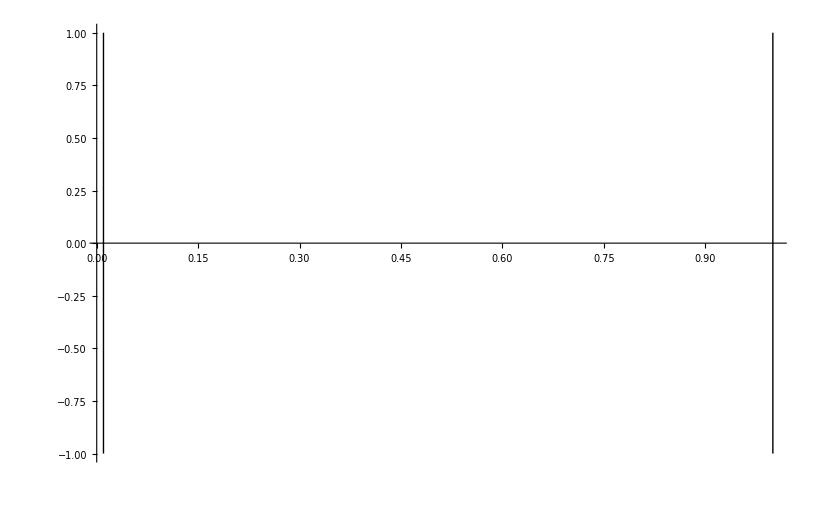

```mathematica
(*Plot all components of the phase space*)
Show[FFS2EPts,FPShow2EPts,Acc2EPts1, Acc2EPts2,Sepx,Traj2EPts,PlotRange->{{ℛ,1},{-1,1}}]
```

```mathematica
FPShow2EPts3D=ListPointPlot3D[{{xTwoEinsteinPointsq1[[1]],0,z[xTwoEinsteinPointsq1[[1]],q1,ℛ]},{xTwoEinsteinPointsq1[[2]],0,z[xTwoEinsteinPointsq1[[2]],q1,ℛ]},{xTwoEinsteinPointsq1[[3]],0,z[xTwoEinsteinPointsq1[[3]],q1,ℛ]},{ℛ,Sqrt[ℛ/3],z[ℛ,q1,ℛ]},{ℛ,-Sqrt[ℛ/3],z[ℛ,q1,ℛ]},{1,Sqrt[1/3],z[1,q1,ℛ]},{1,-Sqrt[1/3],z[1,q1,ℛ]}},PlotStyle->{Black}]
```

FindRoot::nlnum: The function value {-0.05+z[0.025,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.025}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.025}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.26+z[0.13,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {0.13}.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,0.13}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-2.+z[1.,7.,0.01]} is not a list of numbers with dimensions {1} at {x} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x,q1,ℛ]==0,{x,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Accn3D=ContourPlot3D[(1/6)*(2*x-z)==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}, ContourStyle->{Red,Opacity[0.3], Thick}]
```

-Graphics3D-

```mathematica
Dcn3D=ContourPlot3D[(1/6)*(2*x-z)==-0.1,{x,ℛ,1},{y,-1,1},{z,0,2.2}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

```mathematica
(*Accn3D=Plot3D[(1/6)*(2*x-z[x,q1,ℛ]),{x,ℛ,1},{y,-1,1},PlotStyle -> {Red, Opacity[0.25]},Mesh->False,PlotPoints->100]*)
```

```mathematica
Acc=ContourPlot3D[f[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}]
```

ContourPlot3D[f[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}]

```mathematica
Surface=ParametricPlot3D[{x,y,z[x,q1,ℛ]},{x,ℛ,1},{y,-1,1},PlotStyle -> {{Yellow, Opacity[0.4]}},AxesLabel->{"x","y","z"},Mesh->None,PlotRange->{{0.01,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*FFS*)
FFS3D=ParametricPlot3D[{{x,Sqrt[(1/3)*(x+z)],z},{x,-Sqrt[(1/3)*(x+z)],z}},{x,ℛ,1},{z,0,2.2},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.2]}}]
```

-Graphics3D-

```mathematica
Show[Accn3D,Acc,Surface,FPShow2EPts3D,AxesLabel->{"x","y","z"}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,ContourPlot3D[f[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}],-Graphics3D-,-Graphics3D-,AxesLabel→{x,y,z}]

## Q = q(x - ℛ)(1 - x)

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z-2*x)
de3:=z'=-3*y*z+q*(x-ℛ)*(1-x)*y
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→2 x},{x→1,y→-1/(√3),z→0},{x→1,y→1/(√3),z→0},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(3 q y (-1+2 x-ℛ) | 3 q (-1+x) (x-ℛ) | 0
1/3 | -2 y | -1/6
q y (1-2 x+ℛ) | -3 z-q (-1+x) (x-ℛ) | -3 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
2 x) | (0 | 3 q (-1+x) (x-ℛ) | 0
1/3 | 0 | -1/6
0 | -6 x-q (-1+x) (x-ℛ) | 0) | (0
-(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)
(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)) | (1/2 | 0 | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | (√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | -(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1)
(1
-1/(√3)
0) | (√3 q (-1+ℛ) | 0 | 0
1/3 | 2/(√3) | -1/6
-(q (-1+ℛ))/(√3) | 0 | √3) | (√3
2/(√3)
√3 q (-1+ℛ)) | (0 | -1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | -(-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(1
1/(√3)
0) | (-√3 q (-1+ℛ) | 0 | 0
1/3 | -2/(√3) | -1/6
(q (-1+ℛ))/(√3) | 0 | -√3) | (-√3
-2/(√3)
-√3 q (-1+ℛ)) | (0 | 1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | (-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (-√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | (2 √ℛ)/(√3) | -1/6
(q (-1+ℛ) √ℛ)/(√3) | 0 | √3 √ℛ) | ((2 √ℛ)/(√3)
√3 √ℛ
-√3 q (-1+ℛ) √ℛ) | (0 | 1 | 0
0 | -1/(2 √3 √ℛ) | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | (6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)
(ℛ
(√ℛ)/(√3)
0) | (√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | -(2 √ℛ)/(√3) | -1/6
-(q (-1+ℛ) √ℛ)/(√3) | 0 | -√3 √ℛ) | (-√3 √ℛ
-(2 √ℛ)/(√3)
√3 q (-1+ℛ) √ℛ) | (0 | 1/(2 √3 √ℛ) | 1
0 | 1 | 0
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | -(6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)

```mathematica
Eq1[q_,ℛ_]=de1;
Eq2[ℛ_]=de2;
Eq3[q_,ℛ_]=de3;
```

```mathematica
Manipulate[StreamPlot3D[{Eq1[q,ℛ],Eq2[ℛ],Eq3[q,ℛ]},{x,0,1},{y,-1,1},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,5,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,Extra…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$56582,System`VectorPlotsDump`linesxmax$56582},{System`VectorPlotsDump`linesymin$56582,System`VectorPlotsDump`linesymax$56582},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$56582,System`VectorPlotsDump`linesfieldmax$56582}} and System`VectorPlotsDump`extremes$56644 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$56582,System`VectorPlotsDump`linesxmax$56582},{System`VectorPlotsDump`linesymin$56582,System`VectorPlotsDump`linesymax$56582},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$56582,System`VectorPlotsDump`linesfieldmax$56582}} and System`VectorPlotsDump`extremes$56720 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$56582'[System`VectorPlotsDump`t$56582]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$56582[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$56582,System`VectorPlotsDump`linesxmax$56582},{System`VectorPlotsDump`linesymin$56582,System`VectorPlotsDump`linesymax$56582},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$56582,System`VectorPlotsDump`linesfieldmax$56582}} and System`VectorPlotsDump`extremes$56800 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13628,System`VectorPlotsDump`linesxmax$13628},{System`VectorPlotsDump`linesymin$13628,System`VectorPlotsDump`linesymax$13628},«1»,{System`VectorPlotsDump`linesfieldmin$13628,System`VectorPlotsDump`linesfieldmax$13628}} and System`VectorPlotsDump`extremes$13691 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$13628'[System`VectorPlotsDump`t$13628]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$13628[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$13628'[System`VectorPlotsDump`t$13628]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$13628[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13628,System`VectorPlotsDump`linesxmax$13628},{System`VectorPlotsDump`linesymin$13628,System`VectorPlotsDump`linesymax$13628},«1»,{System`VectorPlotsDump`linesfieldmin$13628,System`VectorPlotsDump`linesfieldmax$13628}} and System`VectorPlotsDump`extremes$13764 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$13628'[System`VectorPlotsDump`t$13628]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$13628[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] and NDSolveValue[{System`VectorPlotsDump`w$13628'[System`VectorPlotsDump`t$13628]=={Eq1[0,0],Eq2[0],Eq3[0,0],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$13628[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→«9»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13628,System`VectorPlotsDump`linesxmax$13628},{System`VectorPlotsDump`linesymin$13628,System`VectorPlotsDump`linesymax$13628},«1»,{System`VectorPlotsDump`linesfieldmin$13628,System`VectorPlotsDump`linesfieldmax$13628}} and System`VectorPlotsDump`extremes$13842 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*System of differential equations for x and z -> time variable is lna*)
dex:=x'=-3*q*(x-ℛ)*(1-x)
dez:=z'=-3*z+q*(x-ℛ)*(1-x)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→1,z→0},{x→ℛ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(3 q (-1+2 x-ℛ) | 0
q (1-2 x+ℛ) | -3)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (-3 q (-1+ℛ) | 0
q (-1+ℛ) | -3) | (-3
-3 q (-1+ℛ)) | (0 | 1
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | 1)
(ℛ
0) | (3 q (-1+ℛ) | 0
q-q ℛ | -3) | (-3
3 q (-1+ℛ)) | (0 | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | 1)

```mathematica
Eqx[q_,ℛ_]=dex;
Eqz[q_,ℛ_]=dez;
```

```mathematica
Manipulate[StreamPlot[{Eqz[q,ℛ],Eqx[q,ℛ]},{z,-.2,1},{x,ℛ,1},FrameLabel->{"z","x"}],{q,0,1,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

### Compact Phase Plot

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
de1t:=x'[t]==-3*Y[t]*q*(x[t]-ℛ)*(1-x[t])/((1-Y[t]^2)^(1/2))
de2t:=Y'[t]==-(Y[t]^2)*(1-Y[t]^2)^(1/2)-(((1-Y[t]^2)^(3/2))/6)*((Z[t]/(1-Z[t]))-2*x[t])
de3t:=Z'[t]==-3*Y[t]*Z[t]*(1-Z[t])/((1-Y[t]^2)^(1/2))+q*(1-Z[t])^2*(x[t]-ℛ)*(1-x[t])*Y[t]/((1-Y[t]^2)^(1/2))
```

```mathematica
dext:=x'[t]==-3*q*(x[t]-ℛ)*(1-x[t])
dezt:=z'[t]==-3*z[t]+q*(x[t]-ℛ)*(1-x[t])
```

```mathematica
q=0.01;
ℛ=0.01;
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{de1t,de2t,de3t, x[0]==x0,Y[0]==Y0,Z[0]==Z0}, {x,Y,Z},{t,-500,500}];
```

NDSolve::dvnoarg: The function x appears with no arguments.

```mathematica
sol[1]=traj[0.02,0.01,0.009];
sol[2]=traj[0.02,0.05,0.009];
sol[3]=traj[0.8,0.055,0.009];
sol[4]=traj[0.99,0.06,0.009];
sol[5]=traj[0.02,0.08,0.009];
sol[6]=traj[0.02,0.09,0.009];
```

NDSolve::dvnoarg: The function x appears with no arguments.

```mathematica
ParametricPlot[Evaluate[Table[{x[t],Y[t]}/.sol[i],{i,1,6}], {t,-500,500},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

ReplaceAll::reps: {NDSolve[{(-0.03 (1-x) (-0.01+x))[t]==-(0.03 (1-x[«1»]) (-0.01+x[t]) Y[t])/(√(1+Times[«2»])),Y'[t]==-Y[«1»]^2 √Plus[«2»]-1/6 Plus[«2»]^(3/2) (Times[«2»]+Times[«2»]),Z'[t]==(0.01 «3» Plus[«1»]^2)/(√Plus[«2»])-(3 Y[t]«1»(«1»«1» Z[t])/(√Plus[«2»]),x[0]==0.02,Y[0]==0.01,Z[0]==0.009},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{(-0.03 (1-x) (-0.01+x))[t]==-(0.03 (1-x[«1»]) (-0.01+x[t]) Y[t])/(√(1+Times[«2»])),Y'[t]==-Y[«1»]^2 √Plus[«2»]-1/6 Plus[«2»]^(3/2) (Times[«2»]+Times[«2»]),Z'[t]==(0.01 «3» Plus[«1»]^2)/(√Plus[«2»])-(3 Y[t]«1»(«1»«1» Z[t])/(√Plus[«2»]),x[0]==0.02,Y[0]==0.05,Z[0]==0.009},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -499.98 cannot be used as a variable.

NDSolve::dsvar: -479.571 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-